```mathematica
points=()
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

```mathematica
PvTDataEmp= {{2.73,4.1*^-5},{3.067,1.5*^-5},{4.167,6.4*^-6},{4.5,5.6*^-6},{20.6,3.4*^-6},{22.53,3.4*^-6},{24.967,3.4*^-6}}
```

{{2.73,0.000041},{3.067,0.000015},{4.167,6.4×10^-6},{4.5,5.6×10^-6},{20.6,3.4×10^-6},{22.53,3.4×10^-6},{24.967,3.4×10^-6}}

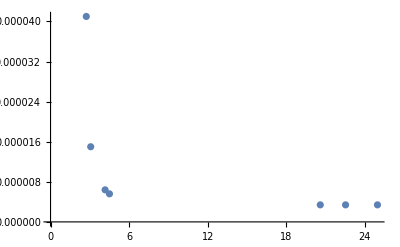

```mathematica
PlotA=ListPlot[PvTDataEmp]
PlotStyle->PointSize[Medium]
```

PlotStyle→PointSize[Medium]

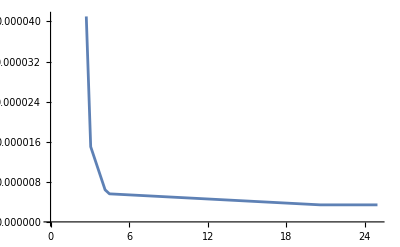

```mathematica
PlotStyle->PointSize[Medium]
PlotB=ListLinePlot[PvTDataEmp]
```

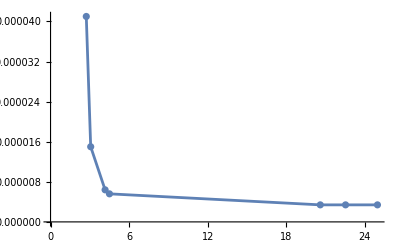

```mathematica
Show[PlotA,PlotB]
```

```mathematica
PvTDataMica={{2+40/60,1.5*^-3},{2+35/60, 1.7*^-5},{3+5/60,7.4*^-6},{3+47/60,4.6*^-6},{5,4*^-6},{8+32/60,3.6*^-6},{12+10+13/60,3.3*^-6}{12+11+38/60,3.2*^-6},{24+5, 3.2*^-6}}
```

{{8/3,0.0015},{31/12,0.000017},{37/12,7.4×10^-6},{227/60,4.6×10^-6},{5,1/250000},{128/15,3.6×10^-6},{945097/1800,1.056×10^-11},{29,3.2×10^-6}}

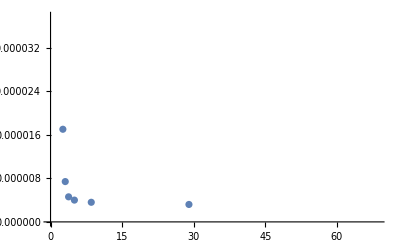

```mathematica
PlotC=ListPlot[PvTDataMica]
PlotStyle->PointSize[Medium]
```

PlotStyle→PointSize[Medium]

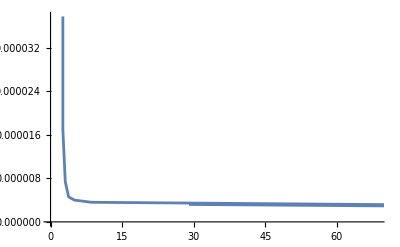

```mathematica
PlotStyle->PointSize[Medium]
PlotD=ListLinePlot[PvTDataMica]
```

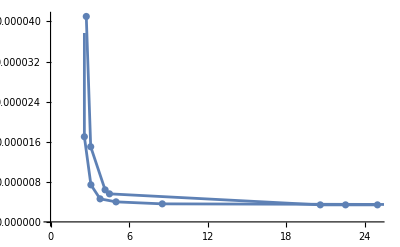

```mathematica
Show[PlotA, PlotB,PlotC,PlotD]
```